Uniform Distribution Example

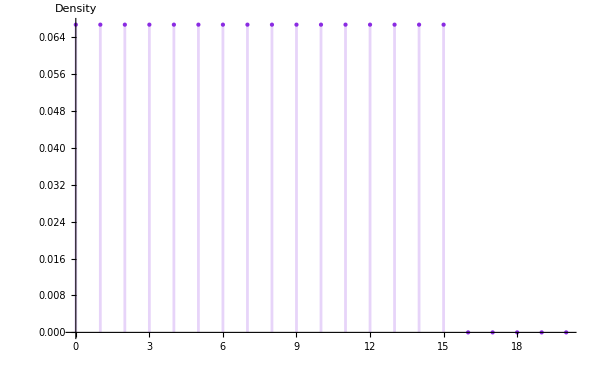
-Graphics-Monthly Claim Counts

```mathematica
Labeled[DiscretePlot[PDF[UniformDistribution[{0,15}],x],{x,0,20},
(*PlotLabel->"Uniform Distribution between 0 and 15",*)
AxesLabel->{"","Density"},
Filling->Axis,
FillingStyle->RGBColor["#8A2BE2"],
Ticks->{Range[0,20],Automatic},
ImagePadding->{{50,50},{10,20}},
ImageSize->{600,400},
AxesOrigin->{0,0},
LabelStyle->{FontSize->14,FontFamily->"Georgia"},
PlotStyle->{
RGBColor["#8A2BE2"],Thick,PointSize[Large]
},
RotateLabel->False
],"Monthly Claim Counts",LabelStyle->{FontSize->14,FontFamily->"Georgia"}]
```

Poisson Distribution Examples

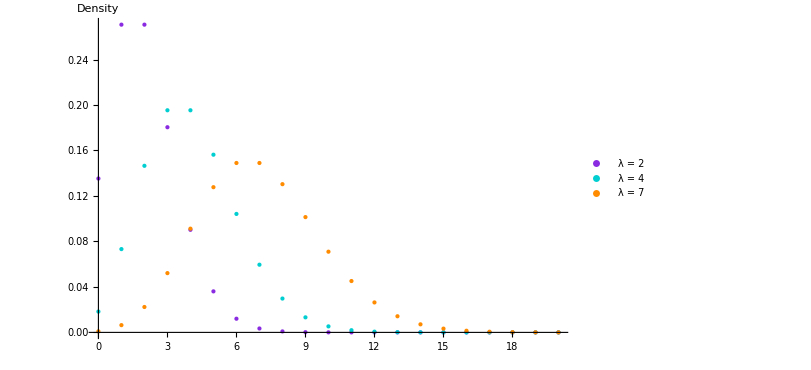
-Graphics-Monthly Claim Counts

```mathematica
Labeled[DiscretePlot[Evaluate@Table[PDF[PoissonDistribution[λ],x],{λ,{2,4,7}}],{x,0,20},
AxesLabel->{"","Density"},
Filling->None,
Ticks->{Range[0,20],Automatic},
ImagePadding->{{50,50},{10,20}},
ImageSize->{600,400},
AxesOrigin->{0,0},
LabelStyle->{FontSize->14,FontFamily->"Georgia"},
PlotStyle->{
{RGBColor["#8A2BE2"],Thick,PointSize[Large]},
{RGBColor["#00CED1"],Thick,PointSize[Large]},
{RGBColor["#FF8C00"],Thick,PointSize[Large]}
},(*Custom colors for each plot*)PlotLegends->Placed[{"λ = 2","λ = 4","λ = 7"},{0.8,0.7}],
RotateLabel->False
],"Monthly Claim Counts",LabelStyle->{FontSize->14,FontFamily->"Georgia"}]
```

Geometric Distribution Examples

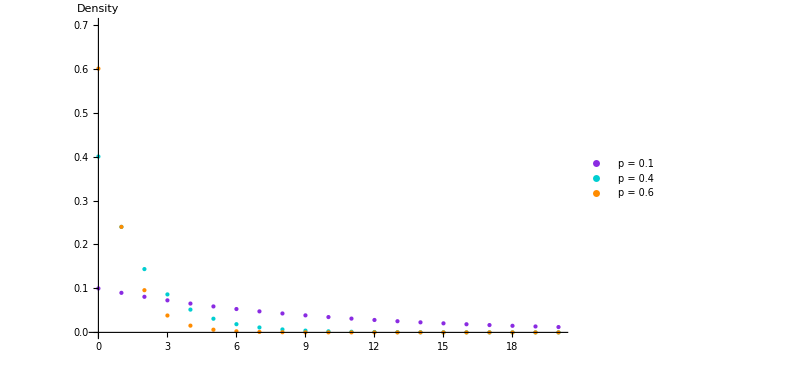
-Graphics-Monthly Claim Counts

```mathematica
Labeled[DiscretePlot[Evaluate@Table[PDF[GeometricDistribution[p],x],{p,{0.1,0.4,0.6}}],{x,0,20},
AxesLabel->{"","Density"},
Filling->None,
Ticks->{Range[0,20],Automatic},
ImagePadding->{{50,50},{20,20}},
ImageSize->{600,400},
AxesOrigin->{0,0},
LabelStyle->{FontSize->14,FontFamily->"Georgia"},
PlotStyle->{
{RGBColor["#8A2BE2"],Thick,PointSize[Large]},
{RGBColor["#00CED1"],Thick,PointSize[Large]},
{RGBColor["#FF8C00"],Thick,PointSize[Large]}
},(*Custom colors for each plot*)PlotLegends->Placed[{"p = 0.1","p = 0.4","p = 0.6"},{0.8,0.7}],
PlotRange->{Automatic,{0,0.7}},
RotateLabel->False
],"Monthly Claim Counts",LabelStyle->{FontSize->14,FontFamily->"Georgia"}]
```

Binomial Distribution Examples

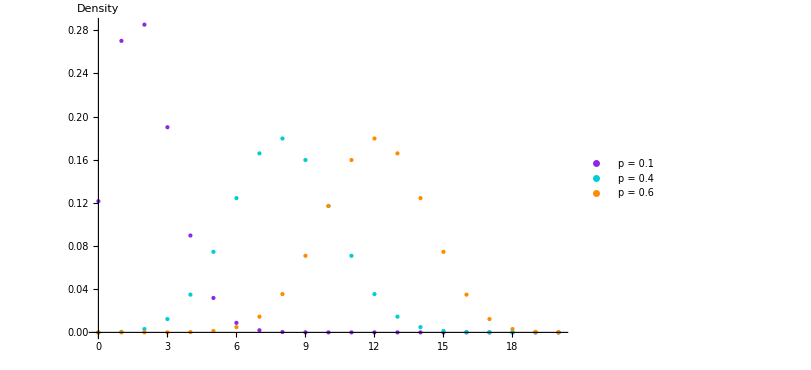
-Graphics-Monthly Claim Counts

```mathematica
Labeled[DiscretePlot[Evaluate@Table[PDF[BinomialDistribution[20,p],x],{p,{0.1,0.4,0.6}}],{x,0,20},
AxesLabel->{"","Density"},
Filling->None,
Ticks->{Range[0,20],Automatic},
ImagePadding->{{50,50},{20,20}},
ImageSize->{600,400},
AxesOrigin->{0,0},
LabelStyle->{FontSize->14,FontFamily->"Georgia"},
PlotStyle->{
{RGBColor["#8A2BE2"],Thick,PointSize[Large]},
{RGBColor["#00CED1"],Thick,PointSize[Large]},
{RGBColor["#FF8C00"],Thick,PointSize[Large]}
},(*Custom colors for each plot*)PlotLegends->Placed[{"p = 0.1","p = 0.4","p = 0.6"},{0.8,0.7}],
RotateLabel->False
],"Monthly Claim Counts",LabelStyle->{FontSize->14,FontFamily->"Georgia"}]
```

Negative Binomial Distribution Examples

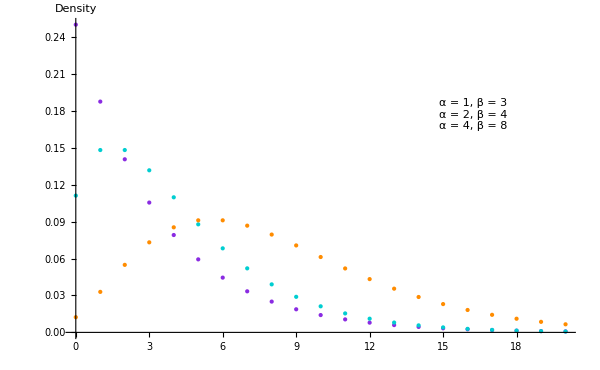
-Graphics-Monthly Claim Counts

```mathematica
dist1=DiscretePlot[PDF[NegativeBinomialDistribution[1,1/(1+3)],x],{x,0,20},PlotStyle->{RGBColor["#8A2BE2"],Thick,PointSize[Large]},Filling->None,
PlotLegends->Placed[Style["α = 1, β = 3",FontSize->14,FontFamily->"Georgia",
FontColor->RGBColor["#8A2BE2"]],
{0.8,0.7}]];

dist2=DiscretePlot[PDF[NegativeBinomialDistribution[2,2/(2+4)],x],{x,0,20},PlotStyle->{RGBColor["#00CED1"],Thick,PointSize[Large]},Filling->None,
PlotLegends->Placed[Style["α = 2, β = 4",FontSize->14,FontFamily->"Georgia",
FontColor->RGBColor["#00CED1"]],
{0.8,0.7}]];

dist3=DiscretePlot[PDF[NegativeBinomialDistribution[4,4/(4+8)],x],{x,0,20},PlotStyle->{RGBColor["#FF8C00"],Thick,PointSize[Large]},Filling->None,
PlotLegends->Placed[Style["α = 4, β = 8",FontSize->14,FontFamily->"Georgia",
FontColor->RGBColor["#FF8C00"]],
{0.8,0.7}]];

Labeled[Show[dist1, dist2, dist3,
AxesLabel->{"","Density"},
Filling->None,
Ticks->{Range[0,20],Automatic},
ImagePadding->{{50,50},{10,20}},
ImageSize->{600,400},
AxesOrigin->{0,0},
LabelStyle->{FontSize->14,FontFamily->"Georgia"},
PlotStyle->{
{RGBColor["#8A2BE2"],Thick,PointSize[Large]},
{RGBColor["#00CED1"],Thick,PointSize[Large]},
{RGBColor["#FF8C00"],Thick,PointSize[Large]}
},
RotateLabel->False
],"Monthly Claim Counts",LabelStyle->{FontSize->14,FontFamily->"Georgia"}]
```

Beta-Binomial Distribution Examples

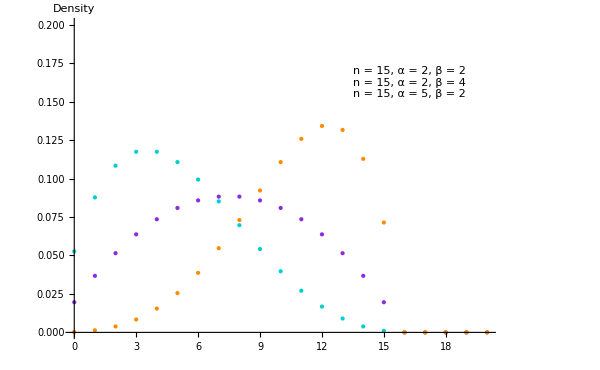
-Graphics-Monthly Claim Counts

```mathematica
dist1=DiscretePlot[PDF[BetaBinomialDistribution[2,2,15],x],{x,0,20},PlotStyle->{RGBColor["#8A2BE2"],Thick,PointSize[Large]},Filling->None,
PlotLegends->Placed[Style["n = 15, α = 2, β = 2",FontSize->14,FontFamily->"Georgia",
FontColor->RGBColor["#8A2BE2"]],
{0.8,0.8}],
PlotRange->{Automatic,{0,0.2}}];

dist2=DiscretePlot[PDF[BetaBinomialDistribution[2,4,15],x],{x,0,20},PlotStyle->{RGBColor["#00CED1"],Thick,PointSize[Large]},Filling->None,
PlotLegends->Placed[Style["n = 15, α = 2, β = 4",FontSize->14,FontFamily->"Georgia",
FontColor->RGBColor["#00CED1"]],
{0.8,0.8}],
PlotRange->{Automatic,{0,0.2}}];

dist3=DiscretePlot[PDF[BetaBinomialDistribution[5,2,15],x],{x,0,20},PlotStyle->{RGBColor["#FF8C00"],Thick,PointSize[Large]},Filling->None,
PlotLegends->Placed[Style["n = 15, α = 5, β = 2",FontSize->14,FontFamily->"Georgia",
FontColor->RGBColor["#FF8C00"]],
{0.8,0.8}],
PlotRange->{Automatic,{0,0.2}}];

Labeled[Show[dist1, dist2, dist3,
AxesLabel->{"","Density"},
Filling->None,
Ticks->{Range[0,20],Automatic},
ImagePadding->{{50,50},{20,20}},
ImageSize->{600,400},
AxesOrigin->{0,0},
LabelStyle->{FontSize->14,FontFamily->"Georgia"},
PlotStyle->{
{RGBColor["#8A2BE2"],Thick,PointSize[Large]},
{RGBColor["#00CED1"],Thick,PointSize[Large]},
{RGBColor["#FF8C00"],Thick,PointSize[Large]}
},
RotateLabel->False
],"Monthly Claim Counts",LabelStyle->{FontSize->14,FontFamily->"Georgia"}]
```